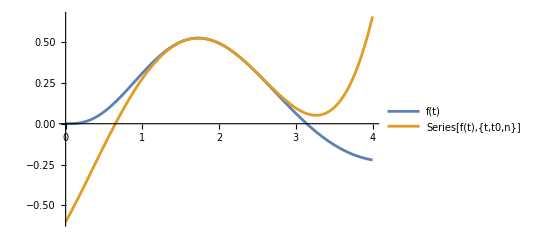

```mathematica
(*Define the function*)f[t_]:=Sin[t] t^2 Exp[-t]

(*Choose the expansion point t0*)
t0=2;

(*Choose the order of Taylor series*)
n=4;

(*Taylor series expansion*)
taylorSeries=Normal[Series[f[t],{t,t0,n}]];

(*Plot the function and its Taylor series approximation*)
Plot[{f[t],taylorSeries},{t,0,4},PlotLegends->{"f(t)",HoldForm[Series[f[t],{t,t0,n}]]/. HoldPattern[Power[t-t0,k_]]:>(t-t0)^k}]

(*Use Manipulate for interactive exploration*)
Manipulate[Module[{approximation},approximation=Normal[Series[f[t],{t,t0,order}]];
Plot[{f[t],approximation},{t,0,4},PlotLegends->{"f(t)",HoldForm[Series[f[t],{t,t0,order}]]/. HoldPattern[Power[t-t0,k_]]:>(t-t0)^k},PlotLabel->Row[{"Order ",order," approximation around t =",t0}]]],{{order,1,"Order:"},1,10,1}]
```